```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/s1220054/Dissertation/Dissertation/DiSamp/src

```mathematica
typelist=Table[Import["type_"<>ToString[i]<>".txt","CSV"],{i,20}]
```

{1}
 |  |  |  |

Part::partw: Part 3 of {0, 0} does not exist. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/General/partw",
ButtonNote->"Part::partw"]

```mathematica
y = 0.0001/(x(x-1))
```

0.0001/((-1+x) x)

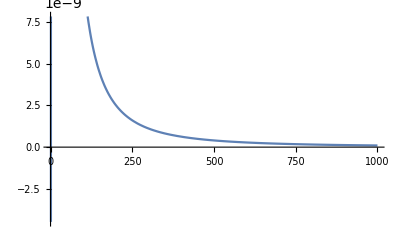

```mathematica
Plot[y,{x,0,1000}]
```

```mathematica
chidata =Import["chi.txt", "CSV"]
```

{{1,38},{2,11},{3,1},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0}}

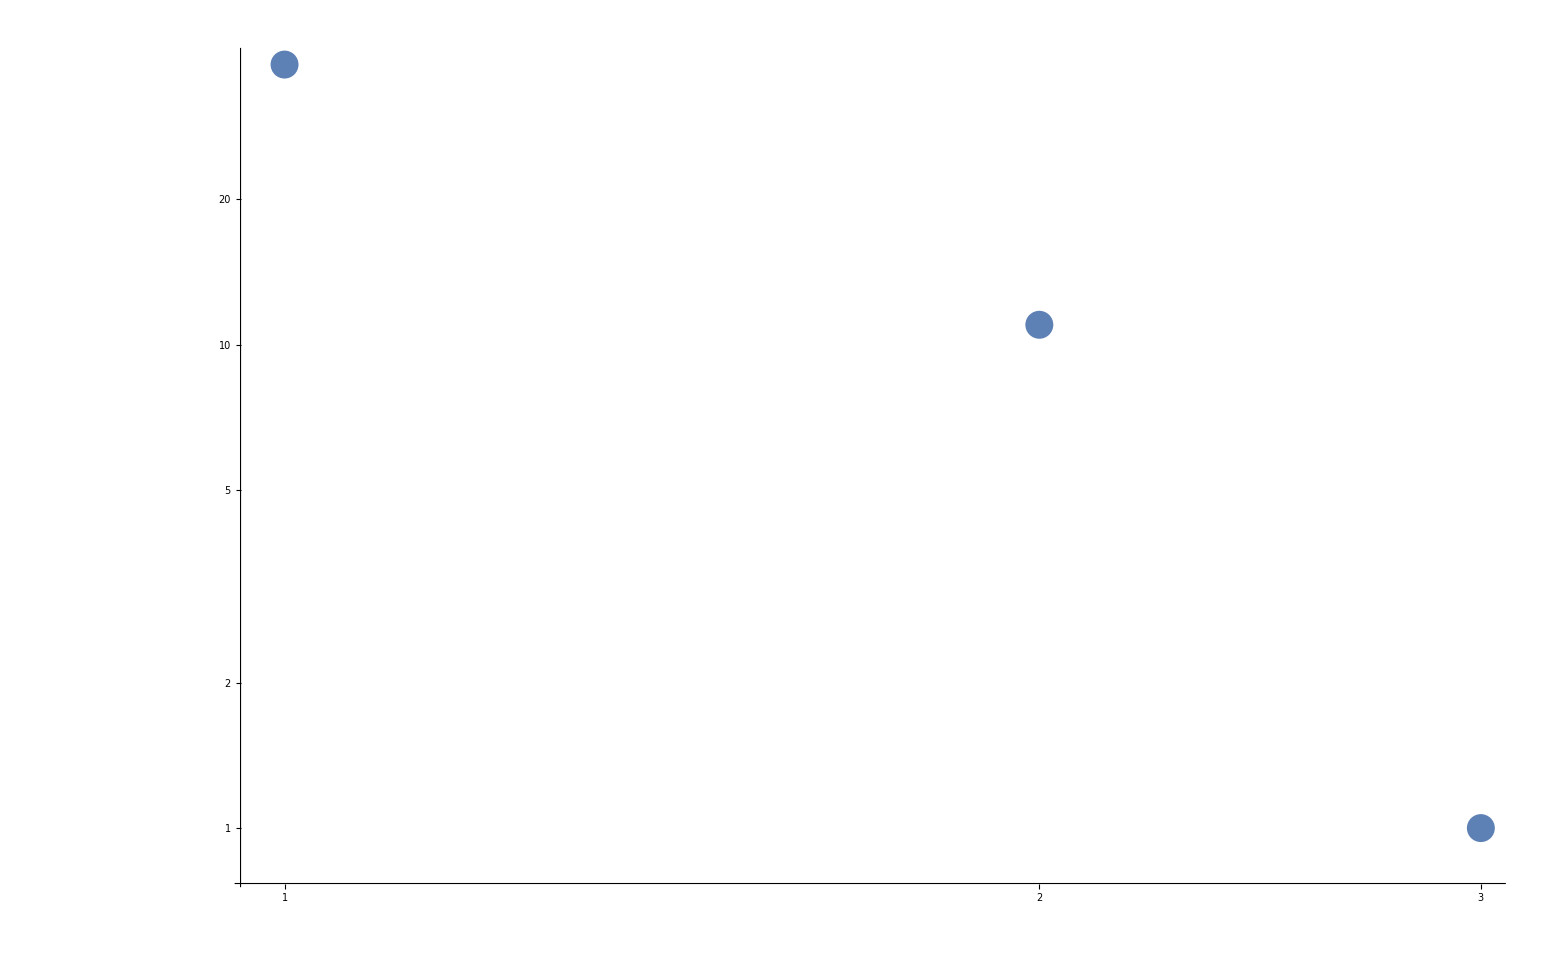

```mathematica
ListLogLogPlot[{chidata},PlotRange->All]
```

```mathematica
datanew=Import["array.txt", "CSV"]
```

{1}
 |  |  |  |

```mathematica
ArrayPlot[datanew]
```

-Graphics-

```mathematica
chinewdata = Import["chinew.txt", "CSV"]
```

{{0,1},{1,20},{2,6},{3,1},{4,1},{5,1},{6,1},{7,1},{8,0},{9,0},{10,0},{11,2},{12,0},{13,2},{14,2},{15,1},{16,0},{17,1},{18,1},{19,0},{20,1},{21,1},{22,0},{23,0},{24,0},{25,0},{26,1},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0}}

```mathematica
dataacc=chinewdata;
dataacc[[All,#2]]=Accumulate[chinewdata[All,#2]]
```

Set::pkspec1: The expression #2 cannot be used as a part specification.

{{0,1},{1,20},{2,6},{3,1},{4,1},{5,1},{6,1},{7,1},{8,0},{9,0},{10,0},{11,2},{12,0},{13,2},{14,2},{15,1},{16,0},{17,1},{18,1},{19,0},{20,1},{21,1},{22,0},{23,0},{24,0},{25,0},{26,1},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0}}[All,All+#2]

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]

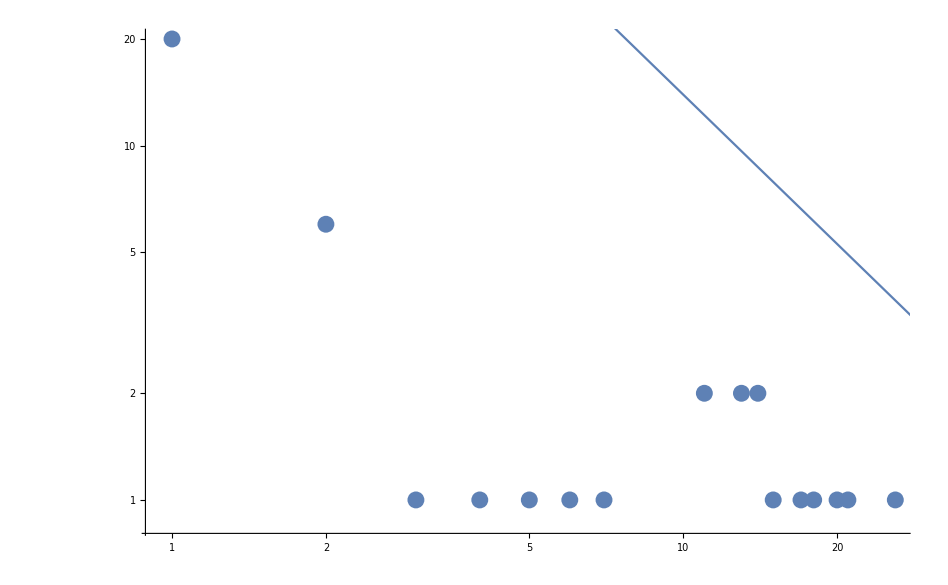

```mathematica
Show[ListLogLogPlot[{chinewdata},PlotRange->All],LogLogPlot[350/(x^1.4),{x,0.5,1000}]]
```